# Exact continuum representation for long-range interacting systems: Higgs spectroscopy of superconductors with long-range interactions

by Andreas A . Buchheit and Torsten Keßler

## Settings

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load MaTex Package. It can be installed by the command:

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
```

## Higgs Oscillations in the s-wave phase

Import data array.  Here we consider 31 points in ν, starting from ν = 1.01 to ν = 3.01.

The following data was created using a high-performance C code. We acknowledge the support of NHR@FAU who granted us access to their supercomputer in order to  generate this data.

We use the following data format: 
1 : time,
2 : ν
3 : C0
4 : U0
5 : DeltaUpUp, s - wave projection (zero, for debugging)
6 : DeltaUpUp, p - wave projection 
7 : DeltaUpUp, d - wave projection (zero, for debugging)
8 : DeltaUpDown, s - wave projection 
9 : DeltaUpDown, p - wave projection
10 : DeltaUpDown, d - wave projection
11 : DeltaDownDown, s - wave projection (zero, for debugging)
12 : DeltaDownDown, p - wave projection 
13 : DeltaDownDown, d - wave projection (zero, for debugging)
14 : Energy
15 : Residuum of fixed point iteration

```mathematica
gapS=ArrayReshape[Import["dataHiggs/classification-higgs-s-wave.dat","Real64"],{31,5000,15}];
```

Quench factor

```mathematica
q=1/100;
```

We depict the arising Higgs oscillations, centered arond their respective mean values.

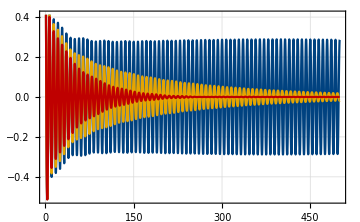

```mathematica
plotHiggs1=ListLinePlot[{1/q*(gapS[[10,All,8]]-Mean[gapS[[10,All,8]]])/Mean[gapS[[10,All,8]]],1/q*(gapS[[16,All,8]]-Mean[gapS[[16,All,8]]])/Mean[gapS[[16,All,8]]],1/q*(gapS[[31,All,8]]-Mean[gapS[[31,All,8]]])/Mean[gapS[[31,All,8]]]},PlotTheme->"Detailed",BaseStyle->{FontFamily->"Latin Modern Roman"},DataRange->{gapS[[1,1,1]],gapS[[1,-1,1]]},PlotLegends->None,FrameStyle->Black,LabelStyle->{FontSize->Scaled[.04],FontFamily->"Helvetica"},FrameLabel->{MaTeX["t/\\tau",Magnification->1.3],MaTeX["(\\Delta_s-\\Delta_\\infty)/(q\\Delta_\\infty)",Magnification->1.3],PlotPoints->500},LabelStyle->{FontFamily->"Helvetica"},ImageSize->Medium,PlotStyle->81]
```

We then provide nonlinear fits to the oscillation maxima, including both an exponential and an algebraic decay.

```mathematica
index=16;
fit1=NonlinearModelFit[Drop[Drop[Drop[FindPeaks[100*(gapS[[index,All,8]]-Mean[gapS[[index,All,8]]])/Mean[gapS[[index,All,8]]]]],-1],1],a*Exp[-r/l]/r^(α),{{α,.2},{l,5000},a},r,MaxIterations->1000000];
```

```mathematica
index=31;
fit2=NonlinearModelFit[Drop[Drop[Drop[FindPeaks[100*(gapS[[index,All,8]]-Mean[gapS[[index,All,8]]])/Mean[gapS[[index,All,8]]]]],-1],1],a*Exp[-r/l]/r^(α),{{α,.2},{l,5000},a},r,MaxIterations->1000000];
```

```mathematica
p1Fit=Plot[{fit1[10t]},{t,1,500},PlotStyle->{Black,Thickness[.004],Dashed},PlotRange->All];
p2Fit=Plot[{fit2[10t]},{t,1,500},PlotRange->All,PlotStyle->{Black,Thickness[.004],Dashed}];
```

We find that the fits reproduce the decay of the oscillation amplitude well.

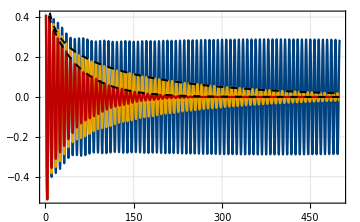

```mathematica
pHiggsFull=Show[plotHiggs1,p1Fit,p2Fit]
```

## Computation of quasi-particle energies

Table of ν values:

```mathematica
nuTab=gapS[[All,1,2]];
```

We compute the minimum of the quasi-particle dispersion energy. To this end, we import the stationary gap after the quench, define the operator E[Δ] and compute it’s minimal trace as a function of k, hence yielding 2 E_min.

```mathematica
TwoEminTab=Table[0,{i,1,31}];
For[i=1,i<=31,i++,
gap=Import["dataHiggs/data-higgs-frequency/nu="<>ToString[nuTab[[i]]]<>"/C0=1.485/U0=0.99/gap-stationary.h5",{"HDF5","Data"}];
gapUU=ListInterpolation[ Map[#["r"]&,"/gap_uu"/.gap,{2}]+I Map[#["i"]&,"/gap_uu"/.gap,{2}],{{-1/2,1/2},{-1/2,1/2}}];gapDD=ListInterpolation[ Map[#["r"]&,"/gap_dd"/.gap,{2}]+I Map[#["i"]&,"/gap_dd"/.gap,{2}],{{-1/2,1/2},{-1/2,1/2}}];gapDU=ListInterpolation[ Map[#["r"]&,"/gap_du"/.gap,{2}]+I Map[#["i"]&,"/gap_du"/.gap,{2}],{{-1/2,1/2},{-1/2,1/2}}];gapUD=ListInterpolation[ Map[#["r"]&,"/gap_ud"/.gap,{2}]+I Map[#["i"]&,"/gap_ud"/.gap,{2}],{{-1/2,1/2},{-1/2,1/2}}];gapMatrix[k1_,k2_]={{gapUU[k1,k2],gapUD[k1,k2]},{gapDU[k1,k2],gapDD[k1,k2]}};energyMatrix[k1_,k2_]:=MatrixPower[(Cos[2Pi*k1]+Cos[2Pi*k2])^2*DiagonalMatrix[{1,1}]+ConjugateTranspose[gapMatrix[k1,k2]].gapMatrix[k1,k2],1/2];
TwoEminTab[[i]]=Min[Min[Table[Tr[energyMatrix[k1,k2]],{k1,-1/2,1/2,1/200},{k2,-1/2,1/2,1/200}]]]]
```

## Computation of Higgs frequencies

The frequencies of the Higgs oscillatins are computed from the respective time dependent data by using a nonlinear fit. Here, both the exponential decay as well as the polynomial decay are being taken into account.

```mathematica
ωHiggsTab=Table[0,{i,1,31}];
```

```mathematica
cutStart=50;
cutEnd=-1;
```

Fit settings

```mathematica
model={c*Cos[ω*t+ϕ]/t^(α)*Exp[-b*t]+ΔInf,b>=0,α>=0};
initialValues={{c,0.002},{ω,0.87},{ϕ,0.5},{α,.15},{b,0.001},{ΔInf,0}};
method=Automatic;
```

```mathematica
ωHiggsTab=ParallelTable[
Quiet[Abs[ω/.NonlinearModelFit[Drop[Drop[Transpose[{gapS[[i,All,{1,8}]][[All,1]],gapS[[i,All,{1,8}]][[All,2]]-Mean[gapS[[i,All,{1,8}]][[All,2]]]}],cutStart],cutEnd],model,initialValues,t,AccuracyGoal->15,PrecisionGoal->15,Method->method,MaxIterations->5000]["BestFitParameters"]]],{i,1,31}
];
```

## Power spectra

We compute power spectra of the Higgs oscillations.

```mathematica
tab1=Transpose[{2Pi/gapS[[10,-1,1]]/TwoEminTab[[10]]*Table[i,{i,1,Length[Drop[Abs[Fourier[gapS[[10,All,{1,8}]][[All,2]]]],1]]}],Drop[Abs[Fourier[gapS[[10,All,{1,8}]][[All,2]]]],1]/Max[Drop[Abs[Fourier[gapS[[10,All,{1,8}]][[All,2]]]],1]]}];
tab2=Transpose[{2Pi/gapS[[16,-1,1]]/TwoEminTab[[16]]*Table[i,{i,1,Length[Drop[Abs[Fourier[gapS[[16,All,{1,8}]][[All,2]]]],1]]}],Drop[Abs[Fourier[gapS[[16,All,{1,8}]][[All,2]]]],1]/Max[Drop[Abs[Fourier[gapS[[16,All,{1,8}]][[All,2]]]],1]]}];
tab3=Transpose[{2Pi/gapS[[31,-1,1]]/TwoEminTab[[31]]*Table[i,{i,1,Length[Drop[Abs[Fourier[gapS[[31,All,{1,8}]][[All,2]]]],1]]}],Drop[Abs[Fourier[gapS[[31,All,{1,8}]][[All,2]]]],1]/Max[Drop[Abs[Fourier[gapS[[31,All,{1,8}]][[All,2]]]],1]]}];
```

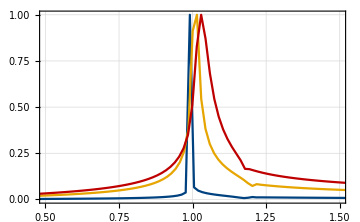

```mathematica
plotHiggsSpectrum=ListLinePlot[{tab1,tab2,tab3},PlotTheme->"Detailed",BaseStyle->{FontFamily->"Latin Modern Roman"},PlotRange->{{0.5,1.5},All},PlotLegends->None,FrameStyle->Black,LabelStyle->{FontSize->Scaled[.04],FontFamily->"Helvetica"},FrameLabel->{MaTeX["\\omega/(2 E_\\text{min})",Magnification->1.3],MaTeX["\\text{power spectrum}~S(\\omega)",Magnification->1.3]},LabelStyle->{FontFamily->"Helvetica"},ImageSize->Medium,PlotStyle->81]
```

Finally, we depict ωHiggs/2Emin as a function of ν:

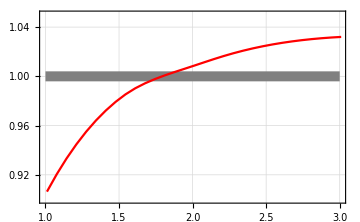

```mathematica
pMode=Show[Plot[1,{ν,1,3},PlotStyle->{Gray,Thickness[.02]},PlotTheme->"Detailed",BaseStyle->{FontFamily->"Latin Modern Roman"},PlotLegends->None,FrameStyle->Black,LabelStyle->{FontSize->Scaled[.04],FontFamily->"Helvetica"},FrameLabel->{MaTeX["\\nu",Magnification->1.3],MaTeX["\\omega_\\text{Higgs}/(2 E_\\text{min})",Magnification->1.3]},LabelStyle->{FontFamily->"Helvetica"},ImageSize->Medium,PlotRange->{.9,1.05}],ListLinePlot[Transpose[{gapS[[All,1,2]],ωHiggsTab/TwoEminTab}],PlotTheme->"Detailed",BaseStyle->{FontFamily->"Latin Modern Roman"},PlotLegends->None,FrameStyle->Black,LabelStyle->{FontSize->Scaled[.04],FontFamily->"Helvetica"},FrameLabel->{MaTeX["\\nu",Magnification->1.3],MaTeX["\\omega_\\text{Higgs}/(2 E_\\text{min})",Magnification->1.3],PlotPoints->500},LabelStyle->{FontFamily->"Helvetica"},ImageSize->Medium,PlotStyle->Red],Epilog->{Text[MaTeX["\\text{stabilization}",Magnification->1.2],Scaled[{0.6,0.32}],{0,0}],Text[MaTeX["\\text{destabilization}",Magnification->1.2],Scaled[{0.25,0.86}],{0,0}]}]
```

Combining all results, we obtain:

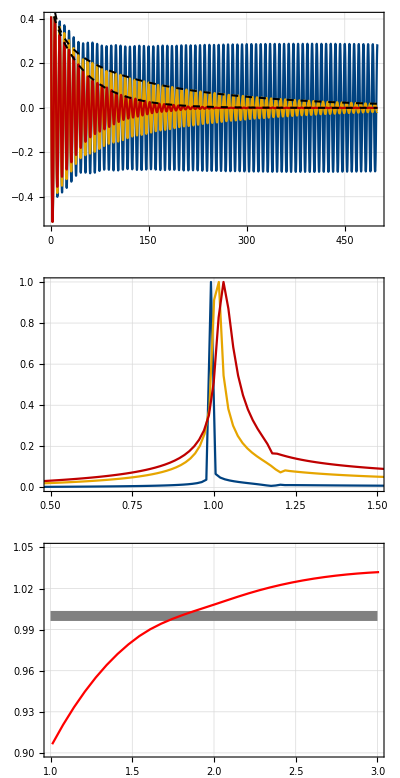

```mathematica
pHiggsFinal=GraphicsColumn[{pHiggsFull,plotHiggsSpectrum,pMode}]
```

```mathematica
(*Export["fig6.png",pHiggsFinal,ImageResolution->600];*)
```